```mathematica
(* A term (final!)*)
Integrate[Exp[I x (s1 s2 - s1)]s1,{s1, 0,1},{s2,0,1}]
```

(1-ⅈ x-Cos[x]+ⅈ Sin[x])/x^2

```mathematica
(* B Term (final!) *)
Integrate[Exp[I x (s1 s2 - s2)](1-s1),{s1, 0,1},{s2,0,1}]
```

```mathematica
-(-1+ⅇ^(-ⅈ x)+ⅈ x)/x^2
```

```mathematica
(* E term (final!)*)
Integrate[Exp[I x (s1 -s1 s2)]s1 ,{s1,0,1},{s2,0,1}]
```

(1-ⅇ^(ⅈ x)+ⅈ x)/x^2

```mathematica
(* F Term (final!)*)
Integrate[Exp[I x (s2 - s1 s2)](1- s1),{s1,0,1}, {s2,0,1}]
```

(1-ⅇ^(ⅈ x)+ⅈ x)/x^2

```mathematica
(* C Term (final!)*)
Integrate[Exp[I x (s1 + s2 - 1)],{s1,0,1},{s2,0,1}]
```

(2-2 Cos[x])/x^2

transition at gamma = ds:0.

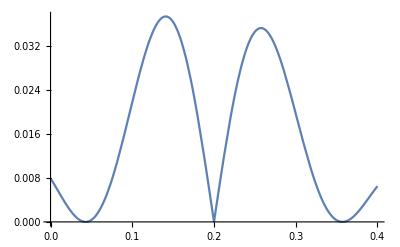

```mathematica
beta = 1;
ds = 0.2;
t = 40;
f[gamma_]:= (4 Sin[(ds - gamma)t/2]^2)/((ds - gamma)^2 t^2)Abs[1 - Exp[beta(ds - gamma)]]
Print["transition at gamma = ds: ", Limit[f[x],{x->ds}]]
Plot[f[x],{x,0,.4}]
```

```mathematica
z[delta_]:=Exp[-(betaE-delta)lambda0] + Exp[-(betaE-delta)lambda1] 
f[delta_]:= Exp[-betaE lambda0]/z[0](1- Exp[-betaE(lambda1 - lambda0)])-Exp[-betaE lambda0 + delta lambda0]/z[delta](1 - Exp[-(betaE-delta)(lambda1 -lambda0)])
```

```mathematica
Series[f[x],{x,0,1}]//FullSimplify
```

(2 ⅇ^(betaE (lambda0+lambda1)) (-lambda0+lambda1) x)/((ⅇ^(betaE lambda0)+ⅇ^(betaE lambda1))^2)+O[x]^2

```mathematica
rat[x_]:=(1 - Exp[-betaE ds])/(1 - Exp[-betaE (ds + x)])
Series[rat[x],{x,0,2}]
```

1-(betaE x)/(-1+ⅇ^(betaE ds))+(betaE^2 (1+ⅇ^(betaE ds)) x^2)/(2 (-1+ⅇ^(betaE ds))^2)+O[x]^3

```mathematica
absInt[g_]:=Abs[1 - Exp[betaE(deltaS -g)]]
Integrate[absInt[g],{g,0,deltaS - deltaMin }, Assumptions -> {deltaS >0, deltaMin>0, betaE >0, deltaMin < deltaS, normH > deltaS + deltaMin}]
Integrate[absInt[g],{g,deltaS + deltaMin ,normH}, Assumptions -> {deltaS >0, deltaMin>0, betaE >0, deltaMin < deltaS, normH > deltaS + deltaMin}]//FullSimplify
```

(betaE deltaMin-betaE deltaS-ⅇ^(betaE deltaMin)+ⅇ^(betaE deltaS))/betaE

-(ⅇ^(-betaE deltaMin)-ⅇ^(betaE (deltaS-normH))+betaE (deltaMin+deltaS-normH))/betaE

```mathematica
FullSimplify[%]
```

-(ⅇ^(-betaE deltaMin)-ⅇ^(betaE (deltaS-normH))+betaE (deltaMin+deltaS-normH))/betaE

```mathematica
Clear[k, beta, betaE,eigs, partfun, rho, rem, sTerm, s]
trunc = 15;
eigs[k_]:= Log[k]
partfun[beta_] := Sum[Exp[-beta * eigs[i]],{i,1, trunc}]
rho[beta_,k_]:= Exp[-beta eigs[k]]/partfun[beta]
rem[beta_,betaE_, k_]:=rho[beta,k] - rho[betaE, k]
sTerm[beta_, betaE_,i_,k_]:= If[i==k,0,rho[beta,i]/(1+Exp[-betaE Abs[eigs[i] - eigs[k]]])-rho[beta,k]/(1 + Exp[betaE Abs[eigs[i]-eigs[k]]])]
s[alpha_,beta_,betaE_, k_] :=alpha N[Sum[sTerm[beta,betaE,i,k],{i,1,trunc}]]
inputMinusOutputDistance[alpha_,beta_,betaE_] := Sum[Abs[rem[beta,betaE,k] + s[alpha,beta,betaE, k]],{k,1,trunc}]
reduction[alpha_,beta_,betaE_]:=inputMinusOutputDistance[alpha, beta,betaE] - Sum[Abs[rem[beta,betaE,k]],{k,1,trunc}]
```

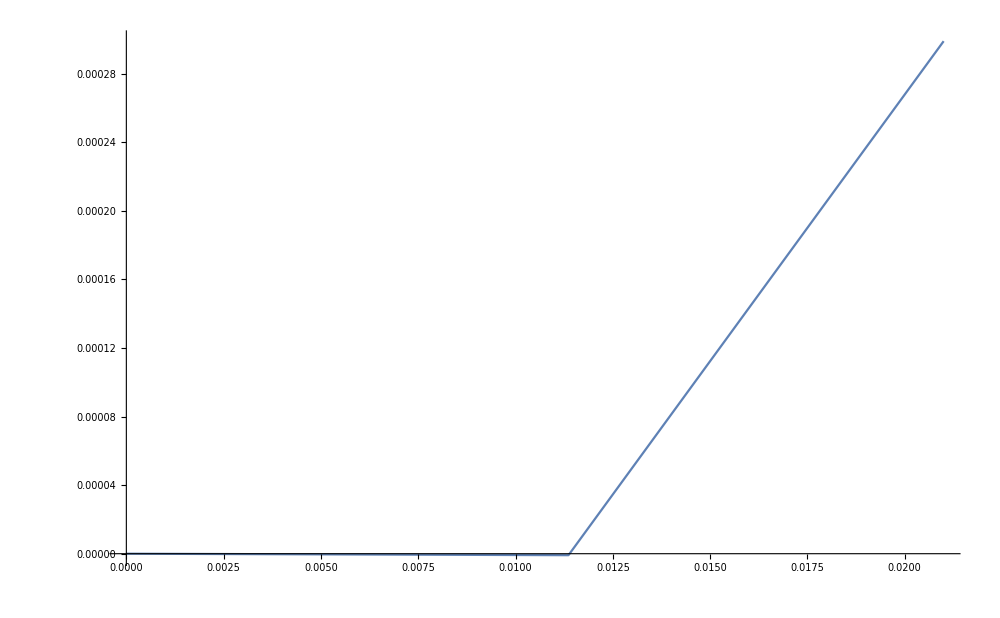

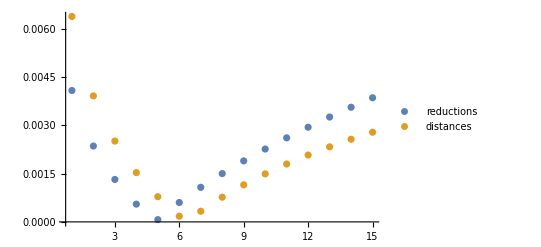

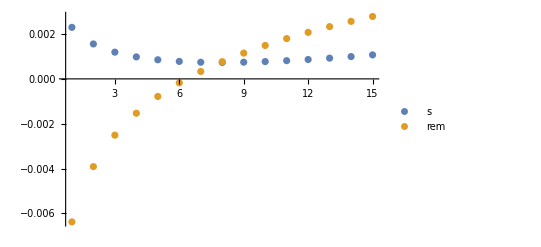

```mathematica
Clear[alpha, beta,betaE]

alpha = 0.05;
beta = 0.0005;
betaE= 0.05;

reductions = Table[Abs[rem[beta,betaE,k] + s[alpha,beta,betaE,k]],{k,1,trunc}];
dists = Table[Abs[rem[beta,betaE,k]],{k,1,trunc}];
Plot[{reduction[x,beta,betaE]},{x,0,0.021},PlotLegends->"Expressions"]

ListPlot[{reductions, dists}, PlotRange->All, PlotLegends->{"reductions","distances"}]
ListPlot[{Table[s[alpha,beta,betaE,k], {k,1,trunc}], Table[rem[beta,betaE,k],{k,1,trunc}]},PlotLegends->{"s","rem"},PlotRange->All]
Clear[alpha, beta,betaE]
```

```mathematica
eps = 10^-3;
NSolve[s[x,beta,betaE,1] - rem[beta,betaE,1] <=eps, x,Reals]
```

NSolve::fulldim: The solution set contains a full-dimensional component; use Reduce for complete solution information.

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{}}

```mathematica
Clear[f, x, beta]
f[x_]:= 1/(1 + x^beta)
Integrate[f[x],{x,l,u}]
```

ConditionalExpression[-l Hypergeometric2F1[1,1/beta,1+1/beta,-l^beta]+u Hypergeometric2F1[1,1/beta,1+1/beta,-u^beta], ]